# SP_L equations

## Interior equations

Expansion of solution in zonal spherical harmonics (1D Legendre polynomials)

```mathematica
ψ[μ_,L_]:=∑_(n=0)^L (2n+1)/2 LegendreP[n,μ] Subscript[ϕ, n][z]
```

```mathematica
L=3;
```

P_n equations (replace Q by ⅆ/ⅆz)

```mathematica
P[n_]=(n+1)/(2n+1)Q Subscript[ϕ, n+1][z] +n/(2n+1)Q Subscript[ϕ, n-1][z]+Subscript[Σ, a,n][z]Subscript[ϕ, n][z]==Subscript[S, n][z]
```

(n Q ϕ_(-1+n)[z])/(1+2 n)+((1+n) Q ϕ_(1+n)[z])/(1+2 n)+ϕ_n[z] Σ_(a,n)[z]==S_n[z]

```mathematica
eqns=Table[P[n]/.If[n≥1, Subscript[S, n][z]->0,Subscript[S, n][z]->Subscript[S, n][z]],{n,0,L}]/.Subscript[ϕ, L+1][z]->0;
```

```mathematica
MatrixForm[eqns]
```

(Q ϕ_1[z]+ϕ_0[z] Σ_(a,0)[z]==S_0[z]
1/3 Q ϕ_0[z]+2/3 Q ϕ_2[z]+ϕ_1[z] Σ_(a,1)[z]==0
2/5 Q ϕ_1[z]+3/5 Q ϕ_3[z]+ϕ_2[z] Σ_(a,2)[z]==0
3/7 Q ϕ_2[z]+ϕ_3[z] Σ_(a,3)[z]==0)

Expansion moments (odd/even)

```mathematica
oddn=Table[2n-1,{n,1,(L+1)/2}];
evenn=Table[2n,{n,1,(L+1)/2}];
```

```mathematica
oddmom=Table[Subscript[ϕ, n][z],{n,0,L}][[evenn]]
evenmom=Table[Subscript[ϕ, n][z],{n,0,L}][[oddn]]
```

{ϕ_1[z],ϕ_3[z]}

{ϕ_0[z],ϕ_2[z]}

Reduction to the “simplified P_L form” (second order eqns.)

express odd moments using the even ones

```mathematica
oddWrtEven=Solve[eqns[[evenn]],oddmom]
```

{{ϕ_1[z]→(-Q ϕ_0[z]-2 Q ϕ_2[z])/(3 Σ_(a,1)[z]),ϕ_3[z]→-(3 Q ϕ_2[z])/(7 Σ_(a,3)[z])}}

insert into the equations

```mathematica
SPL=eqns[[oddn]]/.oddWrtEven[[1]]/.Subscript[S, 0][z]->Subscript[νΣ, f] Subscript[ϕ, 0][z];
```

```mathematica
MatrixForm[SPL]
```

(ϕ_0[z] Σ_(a,0)[z]+(Q (-Q ϕ_0[z]-2 Q ϕ_2[z]))/(3 Σ_(a,1)[z])==νΣ_f ϕ_0[z]
(2 Q (-Q ϕ_0[z]-2 Q ϕ_2[z]))/(15 Σ_(a,1)[z])+ϕ_2[z] Σ_(a,2)[z]-(9 Q^2 ϕ_2[z])/(35 Σ_(a,3)[z])==0)

Definition of “pseudo-fluxes” F_i and “pseudo-diffusion-coefficients” D_i
such that “pseudo-currents” may be defined according to “pseudo-Fick’s-law” as D_(2i+1) ⅆ F_i/ⅆz (here D_i Q F_i)

```mathematica
evenPseudoFluxes=Table[(n+1) Subscript[ϕ, n][z] +(n+2) Subscript[ϕ, n+2][z]==Subscript[F, n][z],{n,0,L,2}]/.Subscript[ϕ, L+1][z]->0
pseudoDiffusions=Table[1/((2n+1)Subscript[Σ, a,n][z])->Subscript[D, n][z],{n,1,L,2}]
```

{ϕ_0[z]+2 ϕ_2[z]==F_0[z],3 ϕ_2[z]==F_2[z]}

{1/(3 Σ_(a,1)[z])→D_1[z],1/(7 Σ_(a,3)[z])→D_3[z]}

Even expansion moments expressed using the even pseudo-fluxes
the zero-th moment is the scalar flux

```mathematica
Table[Subscript[ϕ, 2i][z]/.Solve[Eliminate[evenPseudoFluxes,Drop[evenmom,{i+1}]],Subscript[ϕ, 2i][z]]//First//Expand,{i,0,(L-1)/2}]//MatrixForm
```

(F_0[z]-(2 F_2[z])/3
F_2[z]/3)

Expressing the SP_Nequations in the operator form A {F_i}={b_i}, where the streaming matrix A=diag(ⅆ/ⅆz D_(2i+1)ⅆ/ⅆz)

```mathematica
lower=Table[n/(2n+1),{n,2,L,2}]
centr=Table[(n+1)/(2n+1),{n,0,L,2}]
```

{2/5}

{1,3/5}

```mathematica
Adata=If[L>1,{Band[{2,1}]->lower,Band[{1,1}]->centr},{Band[{1,1}]->centr}];
```

```mathematica
A=SparseArray[Adata,Floor[L/2]+1];
```

```mathematica
A//Normal//MatrixForm
```

(1 | 0
2/5 | 3/5)

```mathematica
rhs=Table[Subscript[Σ, a,n][z]Subscript[ϕ, n][z],{n,0,L,2}];
```

Eliminating the even flux  expansion moments in favor of the unknowns: the even pseudo-fluxes F_i

```mathematica
DelDDelFs=Table[Subscript[DelDDelF, n],{n,0,L,2}];
```

```mathematica
eqnsForDelDDelFs1=Thread[DelDDelFs==LinearSolve[A,rhs]]
```

{DelDDelF_0==ϕ_0[z] Σ_(a,0)[z],DelDDelF_2==1/3 (-2 ϕ_0[z] Σ_(a,0)[z]+5 ϕ_2[z] Σ_(a,2)[z])}

```mathematica
eqnsForDelDDelFs2=Map[Join[{#},evenPseudoFluxes]&,eqnsForDelDDelFs1]
```

{{DelDDelF_0==ϕ_0[z] Σ_(a,0)[z],ϕ_0[z]+2 ϕ_2[z]==F_0[z],3 ϕ_2[z]==F_2[z]},{DelDDelF_2==1/3 (-2 ϕ_0[z] Σ_(a,0)[z]+5 ϕ_2[z] Σ_(a,2)[z]),ϕ_0[z]+2 ϕ_2[z]==F_0[z],3 ϕ_2[z]==F_2[z]}}

```mathematica
eqnsForDelDDelFs3=Map[Eliminate[#,evenmom]&,eqnsForDelDDelFs2]
```

{3 DelDDelF_0+2 F_2[z] Σ_(a,0)[z]==3 F_0[z] Σ_(a,0)[z],-9 DelDDelF_2+4 F_2[z] Σ_(a,0)[z]+5 F_2[z] Σ_(a,2)[z]==6 F_0[z] Σ_(a,0)[z]}

```mathematica
coefAtDs=Thread[Coefficient[eqnsForDelDDelFs3/.Equal->Plus,DelDDelFs]]
```

{3,-9}

```mathematica
eqnsForDelDDelFs4=Thread[Thread[Expand[eqnsForDelDDelFs3[[All,1]]/coefAtDs]]==Thread[Expand[eqnsForDelDDelFs3[[All,2]]/coefAtDs]]]
```

{DelDDelF_0+2/3 F_2[z] Σ_(a,0)[z]==F_0[z] Σ_(a,0)[z],DelDDelF_2-4/9 F_2[z] Σ_(a,0)[z]-5/9 F_2[z] Σ_(a,2)[z]==-2/3 F_0[z] Σ_(a,0)[z]}

```mathematica
eqnsForDelDDelFs5=eqnsForDelDDelFs4/.Thread[DelDDelFs->Table[Subscript[DelDDel, n][z]Subscript[F, n][z],{n,0,L,2}]]
```

{DelDDel_0[z] F_0[z]+2/3 F_2[z] Σ_(a,0)[z]==F_0[z] Σ_(a,0)[z],DelDDel_2[z] F_2[z]-4/9 F_2[z] Σ_(a,0)[z]-5/9 F_2[z] Σ_(a,2)[z]==-2/3 F_0[z] Σ_(a,0)[z]}

Rewriting the equations into a form  m {F_i}-{b_i}==0,  where now the matrix m contains both the streaming and reaction operators

```mathematica
{b,m}=CoefficientArrays[eqnsForDelDDelFs5,Table[Subscript[F, n][z],{n,0,L,2}]]
```

{SparseArray[<0>,{2}],SparseArray[<4>,{2,2}]}

```mathematica
Normal[b]//MatrixForm
```

(0
0)

```mathematica
Normal[m]//MatrixForm
```

(DelDDel_0[z]-Σ_(a,0)[z] | 2/3 Σ_(a,0)[z]
2/3 Σ_(a,0)[z] | DelDDel_2[z]-4/9 Σ_(a,0)[z]-5/9 Σ_(a,2)[z])

Some formal changes to improve readability

```mathematica
F[A_]:=TraditionalForm[A/.{Subscript[DelDDel, n_][z]->Subscript[DelDDel, n],Subscript[Σ, a,n__][z]->Subscript[Σ, n]}]
```

```mathematica
F[Normal[m]//MatrixForm]
```

(DelDDel_0-Σ_0 | (2 Σ_0)/3
(2 Σ_0)/3 | DelDDel_2-(4 Σ_0)/9-(5 Σ_2)/9)

Make sure that in the monoenergetic case, m is symmetric

```mathematica
Normal[m-Transpose[m]]
```

{{0,0},{0,0}}

```mathematica
m2=-Normal[m]/.{Subscript[DelDDel, n_][z]->Subscript[DelDDel, n],Subscript[Σ, a,n__][z]->Subscript[Σ, n]}
```

{{-DelDDel_0+Σ_0,-(2 Σ_0)/3},{-(2 Σ_0)/3,-DelDDel_2+(4 Σ_0)/9+(5 Σ_2)/9}}

```mathematica
m2//MatrixForm
```

(-DelDDel_0+Σ_0 | -(2 Σ_0)/3
-(2 Σ_0)/3 | -DelDDel_2+(4 Σ_0)/9+(5 Σ_2)/9)

```mathematica
MatrixForm[m2/.Subscript[DelDDel, _]->0]
```

(Σ_0 | -(2 Σ_0)/3
-(2 Σ_0)/3 | (4 Σ_0)/9+(5 Σ_2)/9)

```mathematica
Sm=0;
```

```mathematica
For[i=0,i<L,i+=2,
{b,s0}=CoefficientArrays[m2, Subscript[Σ, i]];
c[i]=Flatten[ Normal[s0],{1,3}];
Print[MatrixForm[c[i]]];
Print[Eigenvalues[c[i]]];
Sm=Sm+c[i]
]
```

(1 | -2/3
-2/3 | 4/9)

{13/9,0}

(0 | 0
0 | 5/9)

{5/9,0}

```mathematica
Eigenvalues[Sm]
```

{5/3,1/3}

```mathematica
MatrixForm[Sm]
```

(1 | -2/3
-2/3 | 1)

## Boundary conditions

Legendre expansion of the outgoing partial current

```mathematica
SuperPlus[j]=Table[∫_0^1 LegendreP[n,μ]ψ[μ,L]ⅆμ,{n,1,L,2}]
```

{ϕ_0[z]/4+ϕ_1[z]/2+(5 ϕ_2[z])/16,-1/16 ϕ_0[z]+(5 ϕ_2[z])/16+ϕ_3[z]/2}

expressed using only the even order moments (as in the simplified form of the P_n equations)

```mathematica
SuperPlus[j]=SuperPlus[j]/.oddWrtEven[[1]]
```

{ϕ_0[z]/4+(5 ϕ_2[z])/16+(-Q ϕ_0[z]-2 Q ϕ_2[z])/(6 Σ_(a,1)[z]),-1/16 ϕ_0[z]+(5 ϕ_2[z])/16-(3 Q ϕ_2[z])/(14 Σ_(a,3)[z])}

Extract the equations for pseudo-currents

```mathematica
DDelFs=Table[Subscript[DDelF, n],{n,0,L,2}]
```

{DDelF_0,DDelF_2}

```mathematica
eqnsForDDelFs1=Thread[DDelFs==2Map[Delete[#,-1]&,SuperPlus[j]]]
```

{DDelF_0==2 (ϕ_0[z]/4+(5 ϕ_2[z])/16),DDelF_2==2 (-1/16 ϕ_0[z]+(5 ϕ_2[z])/16)}

Express the boundary equations in terms of only the even expansion moments and pseudo-currents

```mathematica
eqnsForDDelFs2=Map[Join[{#},evenPseudoFluxes]&,eqnsForDDelFs1]
```

{{DDelF_0==2 (ϕ_0[z]/4+(5 ϕ_2[z])/16),ϕ_0[z]+2 ϕ_2[z]==F_0[z],3 ϕ_2[z]==F_2[z]},{DDelF_2==2 (-1/16 ϕ_0[z]+(5 ϕ_2[z])/16),ϕ_0[z]+2 ϕ_2[z]==F_0[z],3 ϕ_2[z]==F_2[z]}}

The final Robin-type boundary conditions

```mathematica
bc1p=Map[Eliminate[#,evenmom]&,eqnsForDDelFs2]
```

{4 F_0[z]-F_2[z]==8 DDelF_0,-3 F_0[z]+7 F_2[z]==24 DDelF_2}

```mathematica
bc2p=Solve[bc1p,DDelFs]//Flatten//Expand
```

{DDelF_0→F_0[z]/2-F_2[z]/8,DDelF_2→-1/8 F_0[z]+(7 F_2[z])/24}

The same as above, only for the incoming partial currents

```mathematica
SuperMinus[j]=Table[∫_-1^0 LegendreP[n,Abs[μ]]ψ[μ,L]ⅆμ//Distribute,{n,1,L,2}]
```

{ϕ_0[z]/4-ϕ_1[z]/2+(5 ϕ_2[z])/16,-1/16 ϕ_0[z]+(5 ϕ_2[z])/16-ϕ_3[z]/2}

```mathematica
SuperMinus[j]=SuperMinus[j]/.oddWrtEven[[1]]
```

{ϕ_0[z]/4+(5 ϕ_2[z])/16-(-Q ϕ_0[z]-2 Q ϕ_2[z])/(6 Σ_(a,1)[z]),-1/16 ϕ_0[z]+(5 ϕ_2[z])/16+(3 Q ϕ_2[z])/(14 Σ_(a,3)[z])}

```mathematica
eqnsForDDelFs1=Thread[DDelFs==-2Map[Delete[#,-1]&,SuperMinus[j]]]
```

{DDelF_0==-2 (ϕ_0[z]/4+(5 ϕ_2[z])/16),DDelF_2==-2 (-1/16 ϕ_0[z]+(5 ϕ_2[z])/16)}

```mathematica
eqnsForDDelFs2=Map[Join[{#},evenPseudoFluxes]&,eqnsForDDelFs1]
```

{{DDelF_0==-2 (ϕ_0[z]/4+(5 ϕ_2[z])/16),ϕ_0[z]+2 ϕ_2[z]==F_0[z],3 ϕ_2[z]==F_2[z]},{DDelF_2==-2 (-1/16 ϕ_0[z]+(5 ϕ_2[z])/16),ϕ_0[z]+2 ϕ_2[z]==F_0[z],3 ϕ_2[z]==F_2[z]}}

```mathematica
bc1m=Map[Eliminate[#,evenmom]&,eqnsForDDelFs2]
```

{-8 DDelF_0+F_2[z]==4 F_0[z],24 DDelF_2+7 F_2[z]==3 F_0[z]}

```mathematica
bc2m=Solve[bc1m,DDelFs]//Flatten//Expand
```

{DDelF_0→-1/2 F_0[z]+F_2[z]/8,DDelF_2→F_0[z]/8-(7 F_2[z])/24}

```mathematica
curs = -DDelFs/.bc2m
```

{F_0[z]/2-F_2[z]/8,-1/8 F_0[z]+(7 F_2[z])/24}

```mathematica
ca=CoefficientArrays[curs,evenmom/.ϕ->F]
```

{SparseArray[<0>,{2}],SparseArray[<4>,{2,2}]}

```mathematica
Normal[ca[[2]]]
```

{{1/2,-1/8},{-1/8,7/24}}

```mathematica
N[Eigenvalues[ca[[2]]]]
```

{0.558547,0.23312}

Albedo boundary conditions

```mathematica
alpha=Solve[γ== (1-α)/(2(1+α)),α][[1]]
```

{α→(1-2 γ)/(1+2 γ)}

```mathematica
aj=Thread[SuperMinus[j]==α SuperPlus[j]]
```

{ϕ_0[z]/4+(5 ϕ_2[z])/16-(-Q ϕ_0[z]-2 Q ϕ_2[z])/(6 Σ_(a,1)[z])==α (ϕ_0[z]/4+(5 ϕ_2[z])/16+(-Q ϕ_0[z]-2 Q ϕ_2[z])/(6 Σ_(a,1)[z])),-1/16 ϕ_0[z]+(5 ϕ_2[z])/16+(3 Q ϕ_2[z])/(14 Σ_(a,3)[z])==α (-1/16 ϕ_0[z]+(5 ϕ_2[z])/16-(3 Q ϕ_2[z])/(14 Σ_(a,3)[z]))}

```mathematica
DDelFsPos=1+(L+1)/2;
```

```mathematica
DDelFsRep=Flatten[Table[{{{i,1,DDelFsPos}}->DDelFs[[i]]/2,{{i,2,2,DDelFsPos}}->-DDelFs[[i]]/2},{i,1,(L+1)/2}]]
```

{{{1,1,3}}→DDelF_0/2,{{1,2,2,3}}→-DDelF_0/2,{{2,1,3}}→DDelF_2/2,{{2,2,2,3}}→-DDelF_2/2}

```mathematica
aj2=ReplacePart[aj,DDelFsRep]
```

{DDelF_0/2+ϕ_0[z]/4+(5 ϕ_2[z])/16==α (-DDelF_0/2+ϕ_0[z]/4+(5 ϕ_2[z])/16),DDelF_2/2-ϕ_0[z]/16+(5 ϕ_2[z])/16==α (-DDelF_2/2-ϕ_0[z]/16+(5 ϕ_2[z])/16)}

```mathematica
eqnsForDDelFs3=Map[Join[{#},evenPseudoFluxes]&,aj2]
```

{{DDelF_0/2+ϕ_0[z]/4+(5 ϕ_2[z])/16==α (-DDelF_0/2+ϕ_0[z]/4+(5 ϕ_2[z])/16),ϕ_0[z]+2 ϕ_2[z]==F_0[z],3 ϕ_2[z]==F_2[z]},{DDelF_2/2-ϕ_0[z]/16+(5 ϕ_2[z])/16==α (-DDelF_2/2-ϕ_0[z]/16+(5 ϕ_2[z])/16),ϕ_0[z]+2 ϕ_2[z]==F_0[z],3 ϕ_2[z]==F_2[z]}}

```mathematica
bc1a=Map[Eliminate[#,evenmom]&,eqnsForDDelFs3]
```

{8 DDelF_0+8 α DDelF_0-F_2[z]+α F_2[z]==(-4+4 α) F_0[z],-24 DDelF_2-24 α DDelF_2-7 F_2[z]+7 α F_2[z]==(-3+3 α) F_0[z]}

```mathematica
bc2a=Solve[bc1a,DDelFs]//Flatten
```

{DDelF_0→(-4 F_0[z]+4 α F_0[z]+F_2[z]-α F_2[z])/(8 (1+α)),DDelF_2→(3 F_0[z]-3 α F_0[z]-7 F_2[z]+7 α F_2[z])/(24 (1+α))}

```mathematica
bc3a=bc2a/.alpha//FullSimplify
```

{DDelF_0→1/4 γ (-4 F_0[z]+F_2[z]),DDelF_2→1/12 γ (3 F_0[z]-7 F_2[z])}

```mathematica
cursa = -DDelFs/.bc3a
```

{-1/4 γ (-4 F_0[z]+F_2[z]),-1/12 γ (3 F_0[z]-7 F_2[z])}

```mathematica
ca=CoefficientArrays[cursa,evenmom/.ϕ->F]
```

{SparseArray[<0>,{2}],SparseArray[<4>,{2,2}]}

```mathematica
Normal[ca[[2]]]//MatrixForm
```

(γ | -γ/4
-γ/4 | (7 γ)/12)

```mathematica
Normal[ca[[2]]/γ]//MatrixForm
```

(1 | -1/4
-1/4 | 7/12)

```mathematica
Eigenvalues[Normal[ca[[2]]]]//N
```

{1.11709 γ,0.46624 γ}

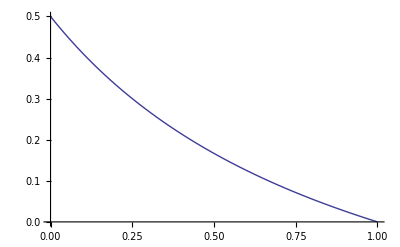

```mathematica
γf[α_]:=(1-α)/(2(1+α));
Plot[γf[α],{α,0,1}]
```